```mathematica
(*Legent
θb - board tilt
ϕr - angle or rotation of the wheel hub with respect to the axis of rotation
ϕt- turing angle
α- contruction angle of the truckv
l2 - the distance by the wheel axis is shifted from the axis of rotation
Δl2 - the graphical variable used to plot some points related to l2
ww - wheel width
w- width of the truck from end to end
wc- position of wheel center on the truck from the extreme 
Δww- for ploting the wheel
ttt - truck to truck lenght
*)

ϕrinit=0;
αinit=45;(*google and find standard values*)
winit=260;(*260*)
diainit = 65;(*65*)
tlinit=95;(*95*)
l2init=100;(*this is a guess*)
l1init=50;(*0.75 % distance from the deck*)
tttinit=920;(*100 *)
wcinit=15;(*15*)
wwinit=50; (*50*)
deckwidthinit=280;
Trucks[α_,w_,dia_,tl_,l2_,l1_,ϕr_,ttt_,wc_,ww_]:=Module[{tr,wheelleft,wheelright,wheel,r,t,AA,BB,CC,DD,wheelleftf,wheelrightf,wheelleftb,wheelrightb,hubf,hubb,wheelcenterleft,wheelcenterright,l2f,l2b,bodyf,bodyb,deck,θb,ϕt},
wheelcenterleft={-w/2+wc,-l2,0};
wheelcenterright={w/2-wc,-l2,0};
hubf={{-w/2,-l2,0},{w/2,-l2,0}};
l2f={{0,-l2,0},{0,0,0}};
wheelleftf={wheelcenterleft+{ww/2,0,0},wheelcenterleft+{-ww/2,0,0}};
wheelrightf={wheelcenterright+{ww/2,0,0},wheelcenterright+{-ww/2,0,0}};
AA={0,0,0};
BB={0,-tl,0};
CC={0,-tl*Cos[α]^2,-tl*Cos[α]*Sin[α]};
DD={0,-l1*Cos[α],-l1*Sin[α]};
bodyf={AA,BB,CC};

r=RotationTransform[α+π/2,{1,0,0}];
l2f=r[l2f];
hubf=r[hubf];
wheelleftf=r[wheelleftf];
wheelrightf=r[wheelrightf];
t=TranslationTransform[DD];
wheelleftf=t[wheelleftf];
wheelrightf=t[wheelrightf];
hubf=t[hubf];
l2f=t[l2f];

(* for the back truck*)
t=TranslationTransform[{0,ttt,0}];
l2b=t[l2f];
bodyb=t[bodyf];
wheelleftb=t[wheelleftf];
wheelrightb=t[wheelrightf];
hubb=t[hubf];
r=RotationTransform[π,{0,0,1}];
l2b=r[l2b];
bodyb=r[bodyb];
wheelleftb=r[wheelleftb];
wheelrightb=r[wheelrightb];
hubb=r[hubb];
(*deck*)
deck={{deckwidthinit/2,0,0},{-deckwidthinit/2,0,0},{-deckwidthinit/2,-ttt,0},{deckwidthinit/2,-ttt,0}};
(*turning*)

r=RotationTransform[ϕr,{0,-Cos[α],-Sin[α]},bodyf[[3]]];
l2f=r[l2f];
hubf=r[hubf];
wheelleftf=r[wheelleftf];
wheelrightf=r[wheelrightf];
r=RotationTransform[-ϕr,{0,Cos[α],-Sin[α]},bodyb[[3]]];
l2b=r[l2b];
hubb=r[hubb];
wheelleftb=r[wheelleftb];
wheelrightb=r[wheelrightb];

(* making ground the referance*)
θb=(wheelleftf[[1]][[3]]-wheelleftf[[2]][[3]])/(wheelleftf[[1]][[1]]-wheelleftf[[2]][[1]]);
θb=ArcTan[θb];
r=RotationTransform[θb,{0,1,0}];
l2b=r[l2b];
hubb=r[hubb];
wheelleftb=r[wheelleftb];
wheelrightb=r[wheelrightb];

l2f=r[l2f];
hubf=r[hubf];
wheelleftf=r[wheelleftf];
wheelrightf=r[wheelrightf];

bodyb=r[bodyb];
bodyf=r[bodyf];
deck=r[deck];


t=TranslationTransform[{0,0,-wheelleftf[[1]][[3]]+dia/2}];
l2b=t[l2b];
hubb=t[hubb];
wheelleftb=t[wheelleftb];
wheelrightb=t[wheelrightb];

l2f=t[l2f];
hubf=t[hubf];
wheelleftf=t[wheelleftf];
wheelrightf=t[wheelrightf];

bodyb=t[bodyb];
bodyf=t[bodyf];
deck=t[deck];

ϕt=(wheelleftf[[1]][[2]]-wheelleftf[[2]][[2]])/-(wheelleftf[[1]][[1]]-wheelleftf[[2]][[1]]);
ϕt=ArcTan[ϕt];
N[θb*180/π];
N[ϕt*180/π];
(*
return=Graphics3D[{Polygon[bodyf],Polygon[bodyb],Blue,Polygon[deck],Red,Cylinder[wheelleftf,dia/2],Red,Cylinder[wheelrightf,dia/2],Red,Cylinder[wheelleftb,dia/2],Red,Cylinder[wheelrightb,dia/2],Thick,Red,Line[hubf],Thick,Red,Line[hubb],Thick,Red,Line[l2f],Thick,Red,Line[l2b]},PlotRange->Automatic,Axes->True,AxesLabel-> {"x","y","z"}];*)
Return[{bodyf,bodyb,deck,wheelleftf,wheelrightf,wheelleftb,wheelrightb,hubf,hubb,l2f,l2b,ϕt*180/π}]



]
```

```mathematica
(*The model shown over here and the actual skateboards that I have are slightly different. The one is the model can be only implemented with tortional string or bushing*)
(* Based on observations it appears as if the  *)
```

```mathematica
Manipulate[
trucks=Trucks[α*π/180,w,dia,tl,l2,l1,ϕr*π/180,ttt,wc,ww];Graphics3D[{Polygon[trucks[[1]]],Polygon[trucks[[2]]],Blue,Polygon[trucks[[3]]],Red,Cylinder[trucks[[4]],dia/2],Red,Cylinder[trucks[[5]],dia/2],Red,Cylinder[trucks[[6]],dia/2],Red,Cylinder[trucks[[7]],dia/2],Thick,Red,Line[trucks[[8]]],Thick,Red,Line[trucks[[9]]],Thick,Red,Line[trucks[[10]]],Thick,Red,Line[trucks[[11]]]},AspectRatio->1,ViewAngle->20°,PlotRange->Automatic,Axes->True,AxesLabel-> {"x","y","z"}]
,{{ϕr,0},-30,30},{{α,αinit},0,90},{{w,winit},50,300},{{dia,diainit},0,100},{{tl,tlinit},25,100},{{l2,l2init},0,100},{{l1,l1init},0,l2},{{ttt,tttinit},300,1500},{{wc,wcinit},0,30},{{ww,wwinit},0,80}]
```

Part::partw: Part 11 of Trucks[π/4, 260, 65, 95, 100, 50, 0, 920, 15, 50] does not exist.

```mathematica
Manipulate[
w=200;
dia=70;
tl=50;
l2=10;
l1=10;
ttt=300;
wc=15;
ww=70;
Plot[Trucks[α*π/180,w,dia,tl,l2,l1,ϕr*π/180,ttt,wc,ww][[12]],{ϕr,-30,30}]
,{{α,45},0,90}]
```

Part::partw: Part 12 of {{{0.`, 0.`, 49.105832357015224`}, {0.`, -50.`, 49.105832357015224`}, {9.448711687585352`, -25.`, 25.960166511226987`}}, « 7 », 40.89374484487072`} does not exist.

Part::partw: Part 12 of {{{0.`, 0.`, 49.1116185242341`}, {0.`, -50.`, 49.1116185242341`}, {9.04968112015939`, -25.`, 25.807042329344167`}}, « 7 », 41.23530423459288`} does not exist.

Part::partw: Part 12 of {{{0.`, 0.`, 49.116661335609635`}, {0.`, -50.`, 49.116661335609635`}, {8.65206827784185`, -25.`, 25.66156136746704`}}, « 7 », 41.56049161537364`} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

Part::partw: Part 12 of Trucks[π/4, 200, 70, 50, 10, 10, -0.523577, 300, 15, 70] does not exist.

Part::partw: Part 12 of Trucks[0.785398, 200., 70., 50., 10., 10., -0.523577, 300., 15., 70.] does not exist.

Part::partw: Part 12 of Trucks[π/4, 200, 70, 50, 10, 10, -0.502206, 300, 15, 70] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

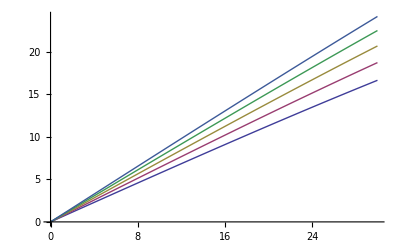

```mathematica
Plot[{Trucks[35*π/180,200,70,50,10,10,ϕr*π/180,300,15,70][[12]],Trucks[40*π/180,200,70,50,10,10,ϕr*π/180,300,15,70][[12]],
Trucks[45*π/180,200,70,50,10,10,ϕr*π/180,300,15,70][[12]],Trucks[50*π/180,200,70,50,10,10,ϕr*π/180,300,15,70][[12]],
Trucks[55*π/180,200,70,50,10,10,ϕr*π/180,300,15,70][[12]]},{ϕr,0,30}]
```

```mathematica
(*Legent
l2 - the distance by the wheel axis is shifted from the axis of rotation
Δl2 - the graphical variable used to plot some points related to l2
ww - wheel width
w- width of the truck from end to end
wc- position of wheel center on the truck from the extreme 
Δww- for ploting the wheel
wr - wheel radius
θb - board tilt
ϕr - angle or rotation of the wheel hub with respect to the axis of rotation
ϕt- turing angle
α- contruction angle of the truckv
ttt - truck to truck lenght
*)

InvertedTrucks[α_,w_,dia_,tl_,l2_,l1_,ϕr_,ttt_,wc_,ww_]:=Module[{tr,wheelleft,wheelright,wheel,r,t,AA,BB,CC,DD,wheelleftf,wheelrightf,wheelleftb,wheelrightb,hubf,hubb,wheelcenterleft,wheelcenterright,l2f,l2b,bodyf,bodyb,deck,θb,ϕt},
wheelcenterleft={-w/2+wc,-l2,0};
wheelcenterright={w/2-wc,-l2,0};
hubf={{-w/2,-l2,0},{w/2,-l2,0}};
l2f={{0,-l2,0},{0,0,0}};
wheelleftf={wheelcenterleft+{ww/2,0,0},wheelcenterleft+{-ww/2,0,0}};
wheelrightf={wheelcenterright+{ww/2,0,0},wheelcenterright+{-ww/2,0,0}};
AA={0,0,0};
BB={0,-tl,0};
CC={0,-tl*Cos[α]^2,-tl*Cos[α]*Sin[α]};
DD={0,-l1*Cos[α],-l1*Sin[α]};
bodyf={AA,BB,CC};

r=RotationTransform[α+π/2,{1,0,0}];
l2f=r[l2f];
hubf=r[hubf];
wheelleftf=r[wheelleftf];
wheelrightf=r[wheelrightf];
t=TranslationTransform[DD];
wheelleftf=t[wheelleftf];
wheelrightf=t[wheelrightf];
hubf=t[hubf];
l2f=t[l2f];

(* for the back truck*)
t=TranslationTransform[{0,ttt,0}];
l2b=t[l2f];
bodyb=t[bodyf];
wheelleftb=t[wheelleftf];
wheelrightb=t[wheelrightf];
hubb=t[hubf];
r=RotationTransform[π,{0,0,1}];
l2b=r[l2b];
bodyb=r[bodyb];
wheelleftb=r[wheelleftb];
wheelrightb=r[wheelrightb];
hubb=r[hubb];

(*Swapping the back truck for the front*)
t=TranslationTransform[{0,-ttt+tl,0}];
l2f=t[l2f];
bodyf=t[bodyf];
wheelleftf=t[wheelleftf];
wheelrightf=t[wheelrightf];
hubf=t[hubf];
t=TranslationTransform[{0,ttt-tl,0}];
l2b=t[l2b];
bodyb=t[bodyb];
wheelleftb=t[wheelleftb];
wheelrightb=t[wheelrightb];
hubb=t[hubb];

(*deck*)
deck={{300/2,0,0},{-300/2,0,0},{-300/2,-ttt,0},{300/2,-ttt,0}};
(*turning*)

r=RotationTransform[ϕr,{0,-Cos[α],-Sin[α]},bodyf[[3]]];
l2f=r[l2f];
hubf=r[hubf];
wheelleftf=r[wheelleftf];
wheelrightf=r[wheelrightf];
r=RotationTransform[-ϕr,{0,Cos[α],-Sin[α]},bodyb[[3]]];
l2b=r[l2b];
hubb=r[hubb];
wheelleftb=r[wheelleftb];
wheelrightb=r[wheelrightb];

(* making ground the referance*)
θb=(wheelleftf[[1]][[3]]-wheelleftf[[2]][[3]])/(wheelleftf[[1]][[1]]-wheelleftf[[2]][[1]]);
θb=ArcTan[θb];
r=RotationTransform[θb,{0,1,0}];
l2b=r[l2b];
hubb=r[hubb];
wheelleftb=r[wheelleftb];
wheelrightb=r[wheelrightb];

l2f=r[l2f];
hubf=r[hubf];
wheelleftf=r[wheelleftf];
wheelrightf=r[wheelrightf];

bodyb=r[bodyb];
bodyf=r[bodyf];
deck=r[deck];


t=TranslationTransform[{0,0,-wheelleftf[[1]][[3]]+dia/2}];
l2b=t[l2b];
hubb=t[hubb];
wheelleftb=t[wheelleftb];
wheelrightb=t[wheelrightb];

l2f=t[l2f];
hubf=t[hubf];
wheelleftf=t[wheelleftf];
wheelrightf=t[wheelrightf];

bodyb=t[bodyb];
bodyf=t[bodyf];
deck=t[deck];

ϕt=(wheelleftf[[1]][[2]]-wheelleftf[[2]][[2]])/-(wheelleftf[[1]][[1]]-wheelleftf[[2]][[1]]);
ϕt=ArcTan[ϕt];
N[θb*180/π];
N[ϕt*180/π];
(*
return=Graphics3D[{Polygon[bodyf],Polygon[bodyb],Blue,Polygon[deck],Red,Cylinder[wheelleftf,dia/2],Red,Cylinder[wheelrightf,dia/2],Red,Cylinder[wheelleftb,dia/2],Red,Cylinder[wheelrightb,dia/2],Thick,Red,Line[hubf],Thick,Red,Line[hubb],Thick,Red,Line[l2f],Thick,Red,Line[l2b]},PlotRange->Automatic,Axes->True,AxesLabel-> {"x","y","z"}];*)
Return[{bodyf,bodyb,deck,wheelleftf,wheelrightf,wheelleftb,wheelrightb,hubf,hubb,l2f,l2b,ϕt*180/π}]



]
```

```mathematica
Manipulate[
trucks=InvertedTrucks[α*π/180,w,dia,tl,l2,l1,ϕr*π/180,ttt,wc,ww];Graphics3D[{Polygon[trucks[[1]]],Polygon[trucks[[2]]],Blue,Polygon[trucks[[3]]],Red,Cylinder[trucks[[4]],dia/2],Red,Cylinder[trucks[[5]],dia/2],Red,Cylinder[trucks[[6]],dia/2],Red,Cylinder[trucks[[7]],dia/2],Thick,Red,Line[trucks[[8]]],Thick,Red,Line[trucks[[9]]],Thick,Red,Line[trucks[[10]]],Thick,Red,Line[trucks[[11]]]},PlotRange->Automatic,Axes->True,AspectRatio->1,ViewAngle->20°,AxesLabel-> {"x","y","z"}]
,{{ϕr,0},-30,30},{{α,45},0,90},{{w,300},50,400},{{dia,200},0,200},{{tl,50},25,100},{{l2,10},0,30},{{l1,10},0,tl*Cos[α*π/180]},{{ttt,900},300,1500},{{wc,15},0,30},{{ww,70},0,80}]
```

Part::partw: Part 11 of InvertedTrucks[π/4, 300, 200, 50, 10, 10, 0, 900, 15, 70] does not exist.

```mathematica
(*Swapping the back truck for the front*)
(*t=TranslationTransform[{0,0,0}];
l2f=t[l2f];
bodyf=t[bodyf];
wheelleftf=t[wheelleftf];
wheelrightf=t[wheelrightf];
hubf=t[hubf];
t=TranslationTransform[{0,0,0}];
l2b=t[l2b];
bodyb=t[bodyb];
wheelleftb=t[wheelleftb];
wheelrightb=t[wheelrightb];
hubb=t[hubb];
*)
```